## Indexed Concatenation & Summarizing Networks

Why we needed some kind of tool to identify and summarize networks

How this new notation works

What else it might be used for?

## Derek Renck, Physics @ Southern, September 2024

## The need to summarize networks, and nested lists of ...

Our group has created enumerations (indexed, ordered lists) of

all strings of all lengths including characters from all writing systems

Find the number of your name in this interactive demonstration: https://demonstrations.wolfram.com/TreeOfStrings/

8512625146879 = 1111011110111111111111111110111101111111111_2  ⇔ “DEREK”

1073471487 = 111111111110111101111111111111_2  ⇔ “KEN”

all lists of all strings (think “books” or “encyclopedias”)

What single number encodes your favorite version of the Bible?

What is the number of the latest edition of the Encyclopaedia Britannica?

all sequential substitution system rulesets (in order to play with all possible “sessie toy universes”)

An example of the process and how it leads to a network

## Index ⇒ Quinary Code ⇒ RuleSet ⇒ Sessie ⇒ Network ⇒ Summary

The “reduced rank” index is mapped to a unique base-5 (quinary) code, which then specifies a unique rule set.

```mathematica
FromReducedRankIndex[253518005]
```

<|Index→253518005,QCode→343233422343,RuleSet→{ABA→AAB,A→ABA}|>

We generate the sessie and its causal network.



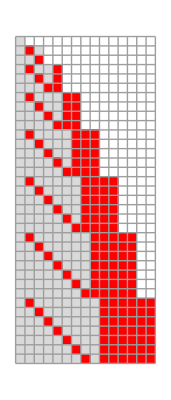
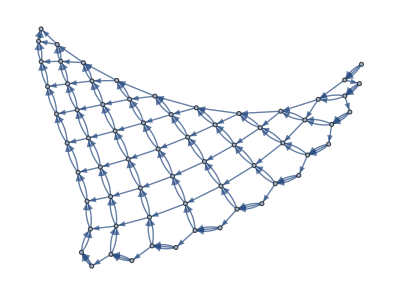
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",400, 
(* options *) SSSMax->35,NetMax->65,NetSize->{Automatic,300},SSSSize->{Automatic,220},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

The code specifies the rule set (laws of nature for the “toy universe”), the initial state string, and how many steps to go.  The colored block images give a quick view of what happens. Internally, it’s all strings of tagged characters, and the network is defined by a list of which nodes are connected:

```mathematica
Short[sss90[["Net"]],4]
```

{1→2,1→2,1→2,2→3,3→4,3→4,3→4,4→5,4→5,2→5,4→6,6→7,6→7,6→7,7→8,7→8,5→8,8→9,8→9,5→9,«1105»,393→394,367→394,394→395,394→395,368→395,395→396,395→396,369→396,396→397,396→397,370→397,397→398,397→398,371→398,398→399,398→399,372→399,399→400,399→400,373→400}

All graph edge information for the network is preserved in the following list:

```mathematica
Short[nds=ToNetDifferenceSets[sss90[["Net"]]],4]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},«363»,{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

We can now either hand it to Colton Davis or to Dr. Caviness’ algorithm to generate an ultra-compact, reduced form. Ta da!

```mathematica
ndsCompact={
IndexedConcatenate[
{1,1,1},{1,1,k+1},
IndexedConcatenate[{1,1,k+2},k-1],
{k+2,k+3},
{k,1,23}
]}
```

{€_(k⊨1)^23[{1,1,1},{1,1,k+1},€^(k-1)[{1,1,k+2}],{k+2,k+3}]}

Notice that this has nested indexed concatenations!   Expanded out:

```mathematica
Short[ExpandAll@ndsCompact,6]
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},«276»,{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{1,1,25},{25,26}}

And expanded back out, it agrees with our network differences set list starting at position 3:

```mathematica
len=Length[ExpandAll@ndsCompact]
ExpandAll@ndsCompact==nds[[3;;len+2]]
```

322

True

## Compare Indexed Concatenation with other familiar notations

Symbolically:

Σ_(i=1)^3 a_i=a_1+a_2+a_3                     ∏_(i=1)^3 a_i=a_1×a_2×a_3=a_1 a_2 a_3                ∪_(i=1)^3 S_i=S_1∪S_2∪S_3

Indexed Concatenation:  €_(i=1)^3 S_i=S_1⧺S_2⧺S_3

Some cases with numbers:

∑_(i=1)^4 i = 1+2+3+4==10                       ∏_(i=1)^3 i = 1 × 2 × 3 = (1)(2)(3) = 6

∪_(i=1)^4{i,i^2}={1,1}∪{2,4}∪{3,9}∪{4,16}={1,2,3,4,9,16}

The union eliminates duplicates and sorts the set, which is not at all what we need:

€_(i=1)^4{i,i^2}={1,1}⧺{2,4}⧺{3,9}⧺{4,16}={1,1,2,4,3,9,4,16}

We settled on the euro symbol, which exists widely, but not in this context, so no misunderstanding should occur.  Visually, it resembles a “C” for “Concatenate”, but also resembles our infix operator “⧺” (taken from the Haskell computer language).

Or should that mean the following, leaving any curly braces in place?

€_(i=1)^4{i,i^2}={1,1}⧺{2,4}⧺{3,9}⧺{4,16}={1,1},{2,4},{3,9},{4,16} ??

Of course, to make a list with sublists, we’d then need to write this as:

{€_(i=1)^4{i,i^2}}={{1,1},{2,4},{3,9},{4,16}}

In that case, how to compress {1,1,2,4,3,9,4,16}?  We may need some sort of disappearing grouping marker:

{€_(i=1)^4｟i,i^2｠}={｟1,1｠⧺｟2,4｠⧺｟3,9｠⧺｟4,16｠}
={｟1,1｠,｟2,4｠,｟3,9｠,｟4,16｠}={1,1,2,4,3,9,4,16}

More simply,

{€_(i=1)^4 i^2}={1⧺4⧺9⧺16}={1,4,9,16}

Will we ever want to “concatenate” integers, placing them side by side, intending 1⧺4⧺9  to mean 149 ?

How about strings?

"ABCABCABC"=€^3"ABC"  ?  or "€^3ABC"  ?  or "€^3｟ABC｠"  ?

{"ABC","ABC","ABC"}= ?

It really seems that "ABC"⧺"ABC"⧺"ABC"should simplify down to "ABCABCABC".

## Examples

The format of IndexedConcatenate implements most of the (single) iterator options allowed for Mathematica functions such as Do, Table, Sum and Product.  The iterator may be completely specified, including variable name, starting and ending values, or some of these can be omitted, if the meaning is clear.

```mathematica
IndexedConcatenate[Subscript[S, i],{i,2,4}]
```

€_(i⊨2)^4 S_i

```mathematica
IndexedConcatenate[Subscript[S, i],{i,2,4}]//Expand
```

S_2⧺S_3⧺S_4

```mathematica
IndexedConcatenate[Subscript[S, i],{i,3}]
```

€_i^3 S_i

```mathematica
IndexedConcatenate[Subscript[S, i],{i,3}]//Expand
```

S_1⧺S_2⧺S_3

```mathematica
IndexedConcatenate[S,3]
```

€^3 S

```mathematica
IndexedConcatenate[S,3]//Expand
```

S⧺S⧺S

IndexedConcatenate objects will not be evaluated unless the Expand or ExpandAll function is applied.

```mathematica
IndexedConcatenate[{i,i^2,i^3},{i,4}]
```

€_i^4{i,i^2,i^3}

```mathematica
Expand[%]
```

{1,1,1,2,4,8,3,9,27,4,16,64}

If nested lists are desired, extra curly braces must be explicitly included.

```mathematica
IndexedConcatenate[{{i,i^2},{i^3,i^4}},{i,3}]
```

€_i^3{{i,i^2},{i^3,i^4}}

```mathematica
ExpandAll[%]
```

{{1,1},{1,1},{2,4},{8,16},{3,9},{27,81}}

In slow motion,

€_i^4{i,i^2,i^3}⇒{1,1,1}⧺{2,4,8}⧺{3,9,27}⧺{4,16,64}
⇒{1,1,1,2,4,8,3,9,27,4,16,64}

€_i^3{{i,i^2},{i^3,i^4}}⇒{{1,1},{1,1}}⧺{{2,4},{8,16}}⧺{{3,9},{27,81}}
⇒{{1,1},{1,1},{2,4},{8,16},{3,9},{27,81}}

The function ReduceSetList attempts to reverse this process, identifying a compact format using IndexedConcatenate objects, possibly nested:

```mathematica
IndexedConcatenate[{{i,i^2}},{i,2,6}]
```

€_(i⊨2)^6{{i,i^2}}

```mathematica
%  //Expand
```

{{2,4},{3,9},{4,16},{5,25},{6,36}}

```mathematica
$debug=True;
ReduceSetList[%184]
```

Entering ReduceSetList with: {{2,4},{3,9},{4,16},{5,25},{6,36}}

exact repLen: 1

exact repLen: 2

Exiting While[...replen...]

Treating Generic patterns

orig: {{2,4},{3,9},{4,16},{5,25},{6,36}}

generic: {{0,0},{0,0},{0,0},{0,0},{0,0}}

generic repLen: 1, pos: {{1,5}}

new varName: n$1

Entering FindSeqFns with:
 parted: {{2,4},{3,9},{4,16},{5,25},{6,36}}
 firstRep: {2,4}

Numerical Table to fit:
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36

Function list: {1+n$1,1+2 n$1+n$1^2}

{{2,4},{3,9},{4,16},{5,25},{6,36}} : {2,4}

{{1},{2}}

{1+n$1,1+2 n$1+n$1^2}

ans: {€_(n$1⊨1)^5{1+n$1,1+2 n$1+n$1^2}}

ExpandAll[ans]: {{2,4,3,9,4,16,5,25,6,36}}

ExpandAll[subseqList]: {{2,4},{3,9},{4,16},{5,25},{6,36}}

(different)

{{2,4},{3,9},{4,16},{5,25},{6,36}}

That’s the same thing, except for the name of the index variable.

Simple repetitions of sets or subsequences of sets of integers require no explicit index variable:

```mathematica
IndexedConcatenate[{1},5]
```

€^5{1}

```mathematica
Expand[%]
```

{1,1,1,1,1}

```mathematica
ReduceSetList[%]
```

{€^5{1}}

IndexedConcatenate objects can be nested:

```mathematica
IndexedConcatenate[
{IndexedConcatenate[{1},3],
IndexedConcatenate[{2},4]},
5]
```

€^5{€^3{1},€^4{2}}

```mathematica
Expand[%]
```

{{1,1,1},{2,2,2,2},{1,1,1},{2,2,2,2},{1,1,1},{2,2,2,2},{1,1,1},{2,2,2,2},{1,1,1},{2,2,2,2}}

```mathematica
{Sequence[1,3,5,7]}
```

{1,3,5,7}

```mathematica
Sequence[Sequence[1,3,5,7]]
```

```mathematica
Sequence[Sequence[1,3,5,7],Sequence[1,3,5,7]]
```

Sequence[1,3,5,7,1,3,5,7]

```mathematica
List[Sequence[1,3,5,7],Sequence[1,3,5,7]]
```

{1,3,5,7,1,3,5,7}

```mathematica
Union[{9},{1,3,5,7},{1,3,5,7}]
```

{1,3,5,7,9}

```mathematica
ReduceSetList[%]
```

{€^5{{1,1,1},{2,2,2,2}}}

```mathematica
Reduce[{{1,1},{2,2,2},{1,1},{2,2,2},{1,1},{2,2,2}}]
```

Reduce::naqs: {1,1}&&{2,2,2}&&{1,1}&&{2,2,2}&&{1,1}&&{2,2,2} is not a quantified system of equations and inequalities.

Reduce[{{1,1},{2,2,2},{1,1},{2,2,2},{1,1},{2,2,2}}]

## A multiply-nested example

```mathematica
{IndexedConcatenate[
{1,5n+4,5n+5},
IndexedConcatenate[
IndexedConcatenate[{1},n],
{1,5n+5+k},
{k,1,4}],
IndexedConcatenate[{1},n-1],
{},
{n,1,8}]}
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€^n[{1}],{1,k+5 n+5}],€^(n-1)[{1}],{}]}

```mathematica
ExpandAll@%
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

For partial expanding, instead of ExpandAll, use Expand and repeat as needed.

```mathematica
Expand@%%
```

{{1,9,10},€^1[{1}],{1,11},€^1[{1}],{1,12},€^1[{1}],{1,13},€^1[{1}],{1,14},€^0[{1}],{},{1,14,15},€^2[{1}],{1,16},€^2[{1}],{1,17},€^2[{1}],{1,18},€^2[{1}],{1,19},€^1[{1}],{},{1,19,20},€^3[{1}],{1,21},€^3[{1}],{1,22},€^3[{1}],{1,23},€^3[{1}],{1,24},€^2[{1}],{},{1,24,25},€^4[{1}],{1,26},€^4[{1}],{1,27},€^4[{1}],{1,28},€^4[{1}],{1,29},€^3[{1}],{},{1,29,30},€^5[{1}],{1,31},€^5[{1}],{1,32},€^5[{1}],{1,33},€^5[{1}],{1,34},€^4[{1}],{},{1,34,35},€^6[{1}],{1,36},€^6[{1}],{1,37},€^6[{1}],{1,38},€^6[{1}],{1,39},€^5[{1}],{},{1,39,40},€^7[{1}],{1,41},€^7[{1}],{1,42},€^7[{1}],{1,43},€^7[{1}],{1,44},€^6[{1}],{},{1,44,45},€^8[{1}],{1,46},€^8[{1}],{1,47},€^8[{1}],{1,48},€^8[{1}],{1,49},€^7[{1}],{}}

```mathematica
Expand@%
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},{1,13},{1},{1,14},{},{1,14,15},{1},{1},{1,16},{1},{1},{1,17},{1},{1},{1,18},{1},{1},{1,19},{1},{},{1,19,20},{1},{1},{1},{1,21},{1},{1},{1},{1,22},{1},{1},{1},{1,23},{1},{1},{1},{1,24},{1},{1},{},{1,24,25},{1},{1},{1},{1},{1,26},{1},{1},{1},{1},{1,27},{1},{1},{1},{1},{1,28},{1},{1},{1},{1},{1,29},{1},{1},{1},{},{1,29,30},{1},{1},{1},{1},{1},{1,31},{1},{1},{1},{1},{1},{1,32},{1},{1},{1},{1},{1},{1,33},{1},{1},{1},{1},{1},{1,34},{1},{1},{1},{1},{},{1,34,35},{1},{1},{1},{1},{1},{1},{1,36},{1},{1},{1},{1},{1},{1},{1,37},{1},{1},{1},{1},{1},{1},{1,38},{1},{1},{1},{1},{1},{1},{1,39},{1},{1},{1},{1},{1},{},{1,39,40},{1},{1},{1},{1},{1},{1},{1},{1,41},{1},{1},{1},{1},{1},{1},{1},{1,42},{1},{1},{1},{1},{1},{1},{1},{1,43},{1},{1},{1},{1},{1},{1},{1},{1,44},{1},{1},{1},{1},{1},{1},{},{1,44,45},{1},{1},{1},{1},{1},{1},{1},{1},{1,46},{1},{1},{1},{1},{1},{1},{1},{1},{1,47},{1},{1},{1},{1},{1},{1},{1},{1},{1,48},{1},{1},{1},{1},{1},{1},{1},{1},{1,49},{1},{1},{1},{1},{1},{1},{1},{}}

Incidentally, this integer set list describes the following network, studied and manually summarized by Colton Davis:

```mathematica
FromNetDifferenceSets[%]
```

{1→2,1→10,1→11,2→3,3→4,3→14,4→5,5→6,5→17,6→7,7→8,7→20,8→9,9→10,9→23,11→12,11→25,11→26,12→13,13→14,14→15,14→30,15→16,16→17,17→18,17→34,18→19,19→20,20→21,20→38,21→22,22→23,23→24,23→42,24→25,26→27,26→45,26→46,27→28,28→29,29→30,30→31,30→51,31→32,32→33,33→34,34→35,34→56,35→36,36→37,37→38,38→39,38→61,39→40,40→41,41→42,42→43,42→66,43→44,44→45,46→47,46→70,46→71,47→48,48→49,49→50,50→51,51→52,51→77,52→53,53→54,54→55,55→56,56→57,56→83,57→58,58→59,59→60,60→61,61→62,61→89,62→63,63→64,64→65,65→66,66→67,66→95,67→68,68→69,69→70,71→72,71→100,71→101,72→73,73→74,74→75,75→76,76→77,77→78,77→108,78→79,79→80,80→81,81→82,82→83,83→84,83→115,84→85,85→86,86→87,87→88,88→89,89→90,89→122,90→91,91→92,92→93,93→94,94→95,95→96,95→129,96→97,97→98,98→99,99→100,101→102,101→135,101→136,102→103,103→104,104→105,105→106,106→107,107→108,108→109,108→144,109→110,110→111,111→112,112→113,113→114,114→115,115→116,115→152,116→117,117→118,118→119,119→120,120→121,121→122,122→123,122→160,123→124,124→125,125→126,126→127,127→128,128→129,129→130,129→168,130→131,131→132,132→133,133→134,134→135,136→137,136→175,136→176,137→138,138→139,139→140,140→141,141→142,142→143,143→144,144→145,144→185,145→146,146→147,147→148,148→149,149→150,150→151,151→152,152→153,152→194,153→154,154→155,155→156,156→157,157→158,158→159,159→160,160→161,160→203,161→162,162→163,163→164,164→165,165→166,166→167,167→168,168→169,168→212,169→170,170→171,171→172,172→173,173→174,174→175,176→177,176→220,176→221,177→178,178→179,179→180,180→181,181→182,182→183,183→184,184→185,185→186,185→231,186→187,187→188,188→189,189→190,190→191,191→192,192→193,193→194,194→195,194→241,195→196,196→197,197→198,198→199,199→200,200→201,201→202,202→203,203→204,203→251,204→205,205→206,206→207,207→208,208→209,209→210,210→211,211→212,212→213,212→261,213→214,214→215,215→216,216→217,217→218,218→219,219→220}

```mathematica
Graph3D[%]
```

-Graphics3D-

#### N.B. How can a list of sets of integers specify a network?!

Look at the first few sets of integers in the list, and the first few network edges:

```mathematica
Short[%%%,2]
```

{{1,9,10},{1},{1,11},{1},{1,12},{1},«208»,{1},{1},{1},{1},{1},{}}

```mathematica
Short[%%%,3]
```

{1→2,1→10,1→11,2→3,3→4,3→14,4→5,5→6,«245»,213→214,214→215,215→216,216→217,217→218,218→219,219→220}

Read that as:

From vertex 1, take 1 step, take 9 steps, and take 10 steps (giving the graph edges 1→2, 1→10, and 1→11, respectively);
From vertex 2, take 1 step (giving the graph edge 2→3);
From vertex 3, take 1 step and take 11 steps (giving the graph edges 3→4 and 3→14, respectively); ...

The list includes one set for each vertex, and then lists how many steps to take for the various graph edges.

## 2D first quadrant, links to neighbors right & above

```mathematica
net2D1Q={1->2,1->3,2->4,2->5,4->7,4->8,7->11,7->12,11->16,11->17,16->22,16->23,22->29,22->30,29->37,29->38,37->46,37->47,3->5,3->6,5->8,5->9,8->12,8->13,12->17,12->18,17->23,17->24,23->30,23->31,30->38,30->39,38->47,38->48,6->9,6->10,9->13,9->14,13->18,13->19,18->24,18->25,24->31,24->32,31->39,31->40,39->48,39->49,10->14,10->15,14->19,14->20,19->25,19->26,25->32,25->33,32->40,32->41,40->49,40->50,15->20,15->21,20->26,20->27,26->33,26->34,33->41,33->42,41->50,41->51,21->27,21->28,27->34,27->35,34->42,34->43,42->51,42->52,28->35,28->36,35->43,35->44,43->52,43->53,36->44,36->45,44->53,44->54,45->54,45->55};
```

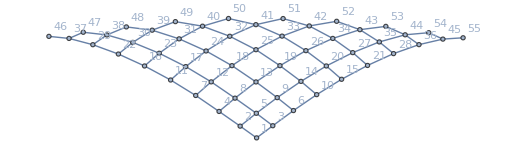

```mathematica
GraphPlot[net2D1Q,VertexLabels->"Name"]
```

A 3D plot lets us turn it to make things a little more clear.

```mathematica
GraphPlot3D[net2D1Q,VertexLabels->"Name"]
```

-Graphics3D-

By the way, the indices here are numbered along diagonal stripes, with a retrace between, a simplification of Georg Cantor’s system for enumerating the rationals.

```mathematica
nsl=ToNetDifferenceSets[net2D1Q]
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

There’s a clear pattern going on here. How well does the attempt at reduction work?

```mathematica
ReduceSetList[nsl]
```

{€_(n$1⊨1)^9[€^n$1[{n$1,n$1+1}]]}

```mathematica
%/.n$1->k
```

{€_(k⊨1)^9[€^k[{k,k+1}]]}

Partly expanded:

```mathematica
Expand[%]
```

{€^1[{1,2}],€^2[{2,3}],€^3[{3,4}],€^4[{4,5}],€^5[{5,6}],€^6[{6,7}],€^7[{7,8}],€^8[{8,9}],€^9[{9,10}]}

Completely expanded:

```mathematica
Expand[%]
```

{{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

## Detailed steps in the ReduceSetList algorithm

```mathematica
$debug=True;
ReduceSetList[nsl]
$debug=False;
```

Entering ReduceSetList with: {{1,2},{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

exact repeating unit length = 1: {{1,2},€^2[{2,3}],€^3[{3,4}],€^4[{4,5}],€^5[{5,6}],€^6[{6,7}],€^7[{7,8}],€^8[{8,9}],€^9[{9,10}]}

Entering ReduceSetList with: {{1,2},€^2[{2,3}],€^3[{3,4}],€^4[{4,5}],€^5[{5,6}],€^6[{6,7}],€^7[{7,8}],€^8[{8,9}],€^9[{9,10}]}

exact repeating unit length: 1, 2, 3, 4

Treating Generic patterns

original: {{1,2},€^2[{2,3}],€^3[{3,4}],€^4[{4,5}],€^5[{5,6}],€^6[{6,7}],€^7[{7,8}],€^8[{8,9}],€^9[{9,10}]}

generic:  {{1,0},€^0[{0,0}],€^0[{0,0}],€^0[{0,0}],€^0[{0,0}],€^0[{0,0}],€^0[{0,0}],€^0[{0,0}],€^0[{0,0}]}

generic repeating unit length: 1, pos: {{2,9}}

Numerical Table to fit:
2 | 3 | 2
3 | 4 | 3
4 | 5 | 4
5 | 6 | 5
6 | 7 | 6
7 | 8 | 7
8 | 9 | 8
9 | 10 | 9

Function list: {1+n$1,2+n$1,1+n$1}

ans: {€_(n$1⊨1)^8[€^(1+n$1)[{1+n$1,2+n$1}]]}

ExpandAll[ans]: {{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

ExpandAll[subseqList]: {{2,3},{2,3},{3,4},{3,4},{3,4},{4,5},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10}}

(same)

generic repeating unit length = 1: {{1,2},€_(n$1⊨1)^8[€^(1+n$1)[{1+n$1,2+n$1}]]}

Entering improveReduction with:    {{1,2},€_(n$1⊨1)^8[€^(1+n$1)[{1+n$1,2+n$1}]]}

Trying to improve reduction at pos: 2 (of {2}")

roll gives same result

No further rolling possible, we're at beginning

Farthest left: {€_(n$1⊨1)^8[€^n$1[{n$1,1+n$1}]],€^9[{9,10}]}

incrementing iterStop: 9

improvement (p was {2}): {€_(n$1⊨1)^9[€^n$1[{n$1,1+n$1}]]}

{€_(n$1⊨1)^9[€^n$1[{n$1,n$1+1}]]}

### Code

#### Code for sessies

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

string::shdw: Symbol string appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

l::shdw: Symbol l appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

s::shdw: Symbol s appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

x$::shdw: Symbol x$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

n$::shdw: Symbol n$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

ans::shdw: Symbol ans appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

ans$::shdw: Symbol ans$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

start::shdw: Symbol start appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

w::shdw: Symbol w appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

l$::shdw: Symbol l$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

d::shdw: Symbol d appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

d$::shdw: Symbol d$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

i::shdw: Symbol i appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

j::shdw: Symbol j appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

j$::shdw: Symbol j$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

wl::shdw: Symbol wl appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

code::shdw: Symbol code appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

wl$::shdw: Symbol wl$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

w$::shdw: Symbol w$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

code$::shdw: Symbol code$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

#### Code to display and evaluate/expand normal and indexed concatenation

```mathematica
Concatenate[l__List] := Join[l];
Format[Concatenate[l__]] := Row[Riffle[{l},"⧺"]];  (* FromCharacterCode[10746] *)
```

```mathematica
Clear[IndexedConcatenate];
Format[IndexedConcatenate[x_, {var_, start_, finish_}]] :=
DisplayForm[RowBox[{UnderoverscriptBox["€", RowBox[{var,"⊨", start}], finish], x }]];  (* FromCharacterCode[8364] *)

Format[IndexedConcatenate[x_, {var_, finish_}]] :=  DisplayForm[RowBox[{UnderoverscriptBox["€", var, finish], x}]];

Format[IndexedConcatenate[x_, finish_]] := DisplayForm[RowBox[{OverscriptBox["€", finish], x}]];
```

```mathematica
Clear[iC];
iC[x_List, iter:(_Integer|{_,_Integer}|{_,_Integer,_Integer})]:=  (Join @@ Table[x,  iter]); 
iC[x_, iter:(_Integer|{_,_Integer}|{_,_Integer,_Integer})]:=  (Concatenate @@ Table[x,  iter]); 
(* allow 1 or more elements to be repeated & concatenated according to iter, result will be a subsequence, assumed to be inside a List *)
iC[x_List] := IndexedConcatenate[x] (* any non-resolved cases redefined, awaiting further processing *)

Unprotect[Expand,ExpandAll];
ExpandAll[x_ /; !FreeQ[x,IndexedConcatenate]] := (x //. IndexedConcatenate->iC);
Expand[x_ /; !FreeQ[x,IndexedConcatenate] ] := (x /. IndexedConcatenate->iC);
Protect[Expand,ExpandAll];
```

#### Code to convert a network to/from its specification as a list of sets of integers, and compact it

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

#### Code to (attempt to) reduce lists to (nested) indexed concatenations

```mathematica
$debug=False;
```

```mathematica
ReduceSetList::usage ="ReduceSetList[l] takes a list l of elements or nested lists of elements, and summarizes duplicate elements and duplicate subsequences using DoConcatenate objects, having the format €_(var=start)^finish[...], specifying how many times the elements or subsequences are repeated.";
```

```mathematica
Clear[FindSeqFns];
FindSeqFns[repLen_Integer,varName_,subseqList_List] := Module[{parted,firstRep,numArray,fnList,ans},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];
parted=Flatten[Partition[subseqList,repLen],1];
firstRep=First@parted;
If[$debug,Print["Entering FindSeqFns with:\n parted: ",parted,"\n firstRep: ",firstRep]];
numArray = Transpose[Cases[#,_Integer,∞]& /@ parted];
If[$debug,Print["\nNumerical Table to fit:\n",Grid@Transpose@numArray]];
fnList=FindSequenceFunction[#,varName]& /@ numArray;

If[$debug,Print["Function list: ",fnList];  Print[parted, " : ",firstRep];  Print@Position[firstRep,_Integer]; 
Print[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]]]];
ans={IndexedConcatenate[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]],{varName,1,Length[subseqList]/repLen}]};
If[$debug,
Print["ans: ",ans]; 
Print["ExpandAll[ans]: ",ExpandAll[ans]]; 
Print["ExpandAll[subseqList]: ",ExpandAll[subseqList]];
Print@If[ExpandAll[ans]===ExpandAll[subseqList],"(same)","(different)"]
];

If[ExpandAll[ans]===ExpandAll[subseqList],ans,subseqList]
];
```

```mathematica
improveReduction[l_List] := Module[{l1=l,l0=l,p},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering improveReduction with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];
p=Flatten@Position[l0,IndexedConcatenate[_,{__}],{1}]; (* find parts that might allow improved reduction *)
(* this only fits indexed concatenate objects with iterators in {...} *)
While[Length[p]>0 && Length[l0]>1,
If[$debug,Print["Trying to improve reduction at pos: ",First[p], " (of ",p,")\nLength[p] = ",Length[p],", Length[l0] = ",Length[l0]]];
l1=improveReductionAt[First[p],l0];
 (* try reducing based on (pos of) first DoConcatentate object *)
If[l1===l0, (* nothing changed, that didn't help *)
p=Rest[p], (* drop first location, try next *)
If[$debug,Print["improvement (p was ",p,"): ",l1]];
l0=l1; p=Flatten@Position[l0,IndexedConcatenate[_,{__}],{1}]; (* if improved, restart from top *)
]; (* end If *)
]; (* end While *)
l1  (* this is now the best we can do *)
];
```

```mathematica
improveReductionAt[k_Integer,l_List] :=
(* Assuming that there is a IndexedConcatenate object at position k in l, "roll" the contents to check that it can actually apply to elements immediately to its left, continuing until it fails. This should pick up cases like €^0{___}, which can't be identified otherwise. *) 
Module[{wholeL,leftL,midEl,rightL,leftLNew,midElNew,rightLNew,leftEltsToDrop,temp,countRolled=0,rollLen,oldArgList,newArgList,iter,iterVar,iterStart,iterStop},
If[k<1||k>Length[l],Print["Error using k=",k,", l=",l];Abort[]];
wholeL=ExpandAll@l;
leftL= Take[l,k-1];                       (* l[[;;k-1]] *)
midEl=l[[k]];
rightL=Drop[l, k];                    (* l[[k+1;;]] *)

If[Head[midEl]=!=IndexedConcatenate,Print["Error: improveReduction called erroneously!"];Break[]
];

While[
(* we'll RollRight the midEl arguments before the iterator, drop the last elt of leftL, prepend an elt to rightL, check against wholeL, and track the countRolled. *)

If[$debug,Print["Before roll attempt: ",wholeL]];

If[Length[leftL]==0,
If[$debug,Print["No further rolling possible, we're at beginning"]];
Break[] (* out of this While loop *)
];
leftLNew =leftL;

oldArgList = Most[List@@midEl];
iter = Last[List@@midEl];
If[Length[iter]==2,iterStart=1,(* if 3 *) iterStart=iter[[2]]];
iterVar=First[iter];
iterStop=Last[iter];

newArgList = RotateRight[oldArgList];  (* roll arg list *)newArgList[[1]] = (newArgList[[1]] /. iter[[1]] ->iter[[1]]-1); (* adj 1st *)
newArgList=FullSimplify[newArgList];

If[$debug,Print["oldArgList: ",oldArgList]];
If[$debug,Print["iter: ",iter," : \n iterVar = ",iterVar,"\n iterStart = ",iterStart,"\n iterStop = ",iterStop]];
If[$debug,Print["newArgList: ",newArgList]];

leftEltsToDrop = ExpandAll@{First[newArgList] /. iterVar -> iterStart};

If[$debug,Print["leftEltsToDrop: ",leftEltsToDrop]];

While[ (* condition is whether we can shift the midEl one space to the left or not giving the same result *)
Length[leftEltsToDrop]>0 && Length[leftLNew]>0 &&
Length[(temp={ExpandAll[Last[leftLNew]]})] <= Length[leftEltsToDrop], 
If[$debug,Print["old value of leftLNew: ",leftLNew]];
leftLNew=Most[leftLNew];                                                                (* drop one term from the leftLNew *)
If[$debug,Print["new value of leftLNew: ",leftLNew]];
If[$debug,Print["dropping last ",Length[temp]," element(s) from leftEltsToDrop: ",leftEltsToDrop]];
leftEltsToDrop = Drop[leftEltsToDrop,-Length[temp]]; 
(* drop the right number of elements from (expanded) list *)
If[$debug,Print["new leftEltsToDrop: ",leftEltsToDrop]];
];
midElNew= IndexedConcatenate[newArgList, iter];
rightLNew = Prepend[rightL,(Last[oldArgList] /. iterVar ->iterStop)]; (* adj 1st *)

countRolled++; (* how many times did we successfully "roll" it? *)

If[$debug,Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew,"\n"]];
(* note that midElNew is just the element IndexedConcatenate, not a subsequence! *)
If[$debug,Print["countRolled: ",countRolled,"\n"]];

If[$debug,
If[wholeL=!=ExpandAll[Join[leftLNew ,{midElNew},rightLNew]],
Print["roll gives different result: "];
Print["wholeL: ",wholeL];
Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew];
Print["new stuff: ",Join[leftLNew ,{midElNew},rightLNew]];
Print["ExpandAll[new stuff]: ",ExpandAll[Join[leftLNew ,{midElNew},rightLNew]]],
Print["roll gives same result"]
]
];
wholeL===ExpandAll[Join[leftLNew ,{midElNew},rightLNew]], 
(* While condition, if it worked, try it again! *)
leftL=leftLNew;
midEl=midElNew;
rightL=rightLNew
];
(* We drop out of the While when the Roll didn't work, so our best answer is: *)
countRolled--; (* back off the count, and we'll use previous leftL, midEl, rightL *)

If[$debug,Print["Farthest left: ",Join[leftL,{midEl},rightL]]];

(* Now find how many elements we can drop from rightL if the index max is increased *)
 
midElNew=midEl;      (* revert, last roll didn't work *)
rightLNew=rightL;   (* revert both *)
newArgList = oldArgList = Most[List@@midEl]; (* revert arg list, too! *)

If[countRolled>=(rollLen=Length[newArgList]),  (* length of indexed subsequence *)
iterStop+=Quotient[countRolled,rollLen];  (* incr iterStop *)
midElNew= IndexedConcatenate[newArgList, {iterVar,iterStart,iterStop}];
(* change index max by # full subseqs *)
If[$debug,Print["dropping ",rollLen * Quotient[countRolled,rollLen]," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen * Quotient[countRolled,rollLen]];  (* drop any full subsequences *)
countRolled -= rollLen * Quotient[countRolled,rollLen];
];
If[$debug,
Print["countRolled: ",countRolled];
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew]
];

rightLNew = SequenceReplace[rightLNew, {IndexedConcatenate[a_,iter1_], IndexedConcatenate[a_,iter2_]}:>
Which[
Head[iter1]===Head[iter2]===Integer, (* reps, no varName *)
List@IndexedConcatenate[a,iter1+iter2],
Head[iter1]===Integer && MatchQ[iter2,{varName_,__Integer}],
List@IndexedConcatenate[a,iter2[[;;-2]] ~Join~ iter2[[3]]+iter1],
Head[iter2]===Integer && MatchQ[iter1,{varName_,__Integer}],
List@IndexedConcatenate[a,iter1[[;;-2]] ~Join~ iter1[[3]]+iter2],
True,
{IndexedConcatenate[a,iter1], IndexedConcatenate[a,iter2]} (* no help! *)
]
]; (* merge neighbors if... *)

If[$debug,
Print["countRolled: ",countRolled];
Print["rightLNew: ",rightLNew]
];

(* check whether we might still have a subsequence from pieces left in rightL *)

While[ (* length possible and it matches *)
rollLen<=Length[rightLNew] && 
(temp=(newArgList /. iterVar-> iterStop+1))===rightLNew[[;;Length[temp]]],
iterStop++;
If[$debug,Print["incrementing iterStop: ", iterStop]];
midElNew= IndexedConcatenate[newArgList, {iterVar,iterStart,iterStop}];
If[$debug,Print["dropping ",rollLen," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen]; (* drop one subseq from rightLNew *)
];

If[$debug,
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew];
];

Join[leftL,{midElNew},rightLNew]  (* leftL won't have changed, but maybe midElNew & rightLNew have *)
];
```

```mathematica
ReduceSetList[l_List]:=Module[{l1,l0=l,gl0,repLen,repMax,pos,varName,i,x,p,len},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering ReduceSetList with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];

(* first check for subsequences of duplicate elements *)

len=Length[l0];
l1=SequenceReplace[l0,
{x:Repeated[a_,{2,len}]}:>IndexedConcatenate[{a},Length[{x}]]
]; (* looks for an exactly repeated subsequence *)

If[l1 =!= l0,(* not same, repLen 1 worked *)
If[$debug,Print["exact repLen = 1: ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
Return[l1]; 
(* if changed, call recursively to continue trying *)
];

If[$debug,Print["exact repLen: ",1]]; (* report what we tried *)
repLen = 2; (* start with length of repeating unit = 2, up to max useful *)
l0=l1; (* set up to check next attempted reduction *)
While[2 repLen <= (len=Length[l1]),
If[$debug,Print["exact repLen: ",repLen]];
l1=SequenceReplace[l1,
{x:Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]}:>
IndexedConcatenate[Take[{x},repLen],Length[{x}]/repLen]
];
If[l1 =!= l0,
If[$debug,Print["Changed (in While): exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];
(* if changed, call recursively to continue reduction, else try next repLen *)
repLen++;
];
If[$debug,Print["Exiting While[...replen...]"]];

If[l1 =!= l0,
If[$debug,Print["Changed: exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];(* if changed, call recursively to continue trying, else try the generic list *)

If[$debug,Print["Treating Generic patterns"]];

repLen = 1;            (* first time choice *)
l0={};                     (* force one time through loop *)

While[l1=!=l0 && Length[l1]>1, (* while changed, and of course, the first time *)
l0=l1;
If[$debug,Print["orig: ",l0]];
len=Length[l0];

gl0=(l0 /. (i_Integer /; i!=1) ->0);

If[$debug,Print["generic: ",gl0]];

pos=SequencePosition[gl0,{Repeated[PatternSequence[x_],{2,len}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];

While[Length[pos]==0 && Length[l0]>1 &&Length[l0]>2*(repLen+1),
repLen++;
pos=SequencePosition[gl0,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];
];

If[pos==0,
If[$debug,Print["Returning, no generic matches found"]];
Return[l0]];  (* No further reduction found *)

(* at least one possible reduction found *)

Do[     (* find first unused variable name of form n$i, where i is an integer *)
varName=ToExpression["n$"<>ToString[i]];
If[FreeQ[l0,varName],Break[]],
{i,1,∞}];

If[$debug,Print["new varName: ",varName]];

l1=Flatten[SequenceSplit[l0,Thread[(Take[l0,#]& /@ pos) -> (FindSeqFns[repLen,varName,Take[l0,#]]& /@ pos)]],1];
If[l1=!=l0, 
If[$debug,Print["generic repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
];
]; (* end of While l1≠l0 loop *)

l1 (* here l1==l0, best we can do *)
];
```

i$::shdw: Symbol i$ appears in multiple contexts {SSS`,Global`}; definitions in context SSS` may shadow or be shadowed by other definitions.

## by Ken Caviness & Derek Renck, Physics @ Southern, September 2024

```mathematica
A ~Concatenate~ B ~Concatenate~ C
```

A⧺B⧺C

# Other cases:

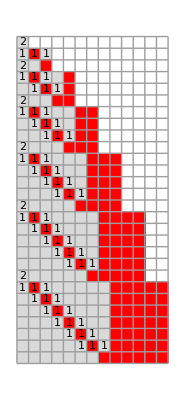
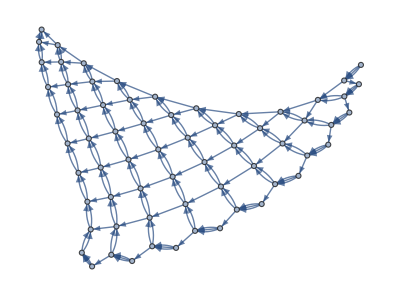
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",150,SSSMax->28,NetMax->65,NetSize->{Automatic,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

```mathematica
sss90nds=ToNetDifferenceSets[sss90[["Net"]]]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12},{1,1,1},{1,1,11},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{12,13},{1,1,1},{1,1,12},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{13,14},{1,1,1},{1,1,13},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{14,15},{1,1,1},{1,1,14},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{15,16},{1,1,1},{1,1,15},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
sss90nds[[1;;-16]]
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12},{1,1,1},{1,1,11},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{12,13},{1,1,1},{1,1,12},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{13,14},{1,1,1},{1,1,13},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{14,15},{1,1,1},{1,1,14},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{15,16},{1,1,1},{1,1,15},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16}}

```mathematica
$debug=False;
ReduceSetList[sss90nds[[1;;-16]]]
$debug=False;
```

{{1,1,1},{1,3},{1,1,1},{1,1,2},{3,4},{1,1,1},€_(n$1⊨1)^2[{1,1,2+n$1}],€_(n$2⊨1)^12[{3+n$2,4+n$2},{1,1,1},{1,1,3+n$2},€^(1+n$2)[{1,1,4+n$2}]]}

```mathematica
%33[[8]]//InputForm
```

IndexedConcatenate[{3 + n$2, 4 + n$2}, {1, 1, 1}, {1, 1, 3 + n$2}, 
 IndexedConcatenate[{1, 1, 4 + n$2}, 1 + n$2], {n$2, 1, 12}]

```mathematica
IndexedConcatenate[
{1, 1, 1}, {1, 1, 1 + n$2}, IndexedConcatenate[{1, 1, 2 + n$2}, n$2-1], {2 + n$2, 3 + n$2}, 
  {n$2, 1, 9}]
```

€_(n$2⊨1)^9[{1,1,1},{1,1,n$2+1},€^(n$2-1)[{1,1,n$2+2}],{n$2+2,n$2+3}]

```mathematica
List@ExpandAll[%]
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12}}

```mathematica
sss90nds[[3;;65]]
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12}}

```mathematica
%38==%43
```

True

Start at node 3

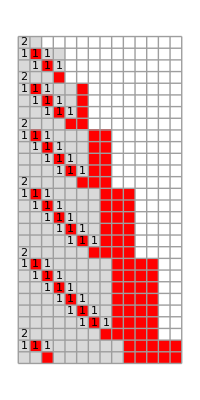
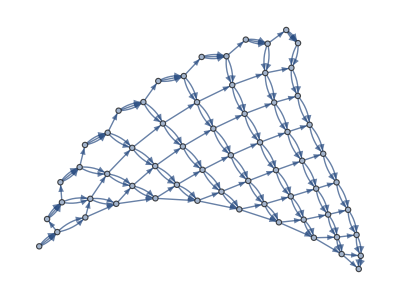
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90s3=SSS[{"ABA"->"AAB","A"->"ABA"}, "AA",150,SSSMax->28,NetMax->63,NetSize->{Automatic,300},SSSSize->{Automatic,220},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True];
```

```mathematica
ToNetDifferenceSets[sss90s3[["Net"]]]
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12},{1,1,1},{1,1,11},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{1,1,12},{12,13},{1,1,1},{1,1,12},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{1,1,13},{13,14},{1,1,1},{1,1,13},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{1,1,14},{14,15},{1,1,1},{1,1,14},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{1,1,15},{15,16},{1,1,1},{1,1,15},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{1,1,16},{16,17},{1,1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
IndexedConcatenate[
{1, 1, 1}, {1, 1, 1 + n$2}, IndexedConcatenate[{1, 1, 2 + n$2}, n$2-1], {2 + n$2, 3 + n$2}, 
  {n$2, 1, 9}]
```

€_(n$2⊨1)^9[{1,1,1},{1,1,n$2+1},€^(n$2-1)[{1,1,n$2+2}],{n$2+2,n$2+3}]

```mathematica
List@ExpandAll[%51]
```

{{1,1,1},{1,1,2},{3,4},{1,1,1},{1,1,3},{1,1,4},{4,5},{1,1,1},{1,1,4},{1,1,5},{1,1,5},{5,6},{1,1,1},{1,1,5},{1,1,6},{1,1,6},{1,1,6},{6,7},{1,1,1},{1,1,6},{1,1,7},{1,1,7},{1,1,7},{1,1,7},{7,8},{1,1,1},{1,1,7},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{1,1,8},{8,9},{1,1,1},{1,1,8},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{1,1,9},{9,10},{1,1,1},{1,1,9},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{1,1,10},{10,11},{1,1,1},{1,1,10},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{1,1,11},{11,12}}

```mathematica
Length[%53]
```

63

```mathematica
%54[[1;;63]]==%53[[1;;63]]
```

True

```mathematica
sss90s3
```

```mathematica
sss90s3[["RuleSet"]]
sss90s3[["Evolution"]][[1]]
sss90s3[["Distance"]]
```

{ABA→AAB,A→ABA}

AA

{0,1,2,2,3,3,3,4,5,4,4,4,6,7,5,5,5,5,8,9,6,6,6,6,6,10,11,7,7,7,7,7,7,12,13,8,8,8,8,8,8,8,14,15,9,9,9,9,9,9,9,9,16,17,10,10,10,10,10,10,10,10,10,18,19,11,11,11,11,11,11,11,11,11,11,20,21,12,12,12,12,12,12,12,12,12,12,12,22,23,13,13,13,13,13,13,13,13,13,13,13,13,24,25,14,14,14,14,14,14,14,14,14,14,14,14,14,26,27,15,15,15,15,15,15,15,15,15,15,15,15,15,15,28,29,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

```mathematica
Tally[sss90s3[["Distance"]]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1}}

```mathematica
Tally[sss90s3[["Distance"]]][[1;;17]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16}}

Best start: “AA”

Reduced Form:

```mathematica
IndexedConcatenate[
{1, 1, 1}, {1, 1, 1 + n$2}, IndexedConcatenate[{1, 1, 2 + n$2}, n$2-1], {2 + n$2, 3 + n$2}, 
  {n$2, 1, ∞}] /. n$2->i
```

€_(i⊨1)^∞[{1,1,1},{1,1,i+1},€^(i-1)[{1,1,i+2}],{i+2,i+3}]